# Unit 6 - Applications of the Derivative (1)

In Units 6 and 7 we are to review some of the many other applications of the derivative covered in Calculus I and II, with the help of Mathematica.

Topics covered in Unit 6 are listed below.

Speed, velocity and acceleration

Implicit differentiation and ContourPlot

Related rates

Taylor polynomials and approximation; Block

Newton’s method

## Speed, velocity and acceleration

Let variable t denote the time elapsed since some reference time t=0, and y=s(t) be the position function that describes the position of a moving object at time t. The position, the velocity, and the acceleration of the object at any moment t can be found by evaluating s(t),s'(t), and s''(t), respectively. The speed of the object at time t is given by the quantity of its velocity. Speed is always non-negative, while velocity can be positive or negative and indicate the direction in which the object moves.

Example 1
A ball is tossed vertically in the air from ground level with an initial velocity of 13 meters per second. Without considering air resistance, its position function is y=s(t)=-4.9 t^2+ 12t.
(a) In how many seconds does the ball attain maximum height?
(b) What is the maximum height?
(c) What is the speed, the velocity, and the acceleration of the ball as it reaches a height of 6 meters going down?
(d) In how many seconds does the ball fall to ground?
(e) Plot the position function together with the velocity and the acceleration functions. Tips: You may use the result from part (d) to determine the interval for Plot.

```mathematica
y[t_]:=-4.9t^2+13t
```

(a) When the velocity is positive, the ball is still going up. When it’s negative, the ball is going down to the ground. When it is zero, the ball attains the maximum height. We don’t know when the velocity y'(t)  is zero. Let Mathematica find the t value for us.

```mathematica
NSolve[y'[t]==0,t]
```

{{t→1.32653}}

```mathematica
tAtMaxY=(t/.%)[[1]] (* Don't just copy and paste. Use computer code to do it. When writing computer program, we must do this way. *)
```

1.32653

(b) Thus, the maximum height is

```mathematica
y[tAtMaxY]
```

8.62245

(c) We need first to know when the ball is at the height of 6 meters.

```mathematica
NSolve[y[t]==6,t]
```

{{t→0.594961},{t→2.0581}}

We got two t values. Why? When t≈0.59, the ball is going upward. And when t≈2.06, the ball is going downward. According to the question, we know t≈0.59.

```mathematica
tAt6=(t/.%)[[1]]
```

0.594961

Now, we can compute the remaining task.

```mathematica
Abs[y'[tAt6]] (* the speed *)
```

7.16938

```mathematica
y'[tAt6] (* the velocity *)
```

7.16938

```mathematica
y''[tAt6] (* the acceleration *)
```

-9.8

(d) When the ball falls to the ground level, the height is zero.

```mathematica
NSolve[y[t]==0]
```

{{t→0.},{t→2.65306}}

Since t=0 refers to the initial status of the ball, the correct answer is t=0.65306.

```mathematica
tBackToGround=(t/.%)[[2]]
```

2.65306

(e) Plot the functions together.

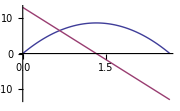

```mathematica
Plot[{y[t],y'[t]},{t,0,tBackToGround},PlotRange->{-13,13},ImageSize->180]
```

The graph shows that
(1) The height of the ball is increasing over (0,1.32653) with the velocity positive, and decreasing over (1.32653,2.65306) with the velocity negative.
(2) The velocity is always decreasing.

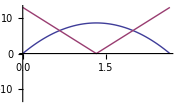

```mathematica
Plot[{y[t],Abs[y'[t]]},{t,0,tBackToGround},PlotRange->{-13,13},ImageSize->180]
```

The graph indicates us that
(1) The speed of the ball is decreasing over (0,1.32653), but increasing over (1.32653,2.65306).
(2) When the speed is zero at t=1.32653, the ball attains the maximum height.

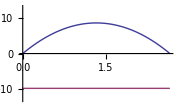

```mathematica
Plot[{y[t],y''[t]},{t,0,tBackToGround},PlotRange->{-13,13},ImageSize->180]
```

We can see that the acceleration of the ball is a constant, -9.8 m/s^2, which means gravitational pull (downward) is the only force applied to the ball.

You may merge these three graphs into one by the command.

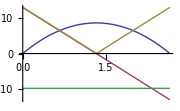

```mathematica
Plot[{y[t],y'[t],Abs[y'[t]],y''[t]},{t,0,tBackToGround},PlotRange->{-13,13},ImageSize->180]
```

## Implicit differentiation and ContourPlot

Before we solve problems involving related rates, we need to know how to do implicit differentiation with Mathematica.

The problem is that, provided x and y satisfy an equation F(x,y)=0, we want to compute (d y)/(d x), where y may or may not be a function of x. With Mathematica, we take the following procedure.

Differentiate the equation F(x,y)=0 with respect to x, using the following command and specifying y  as a function of x.

D[F[x,y[x]]==0,x]

Solve the returned equation from step 1 for y'(x)

Solve[%,y'[x]]

We may combine the two commands into one like

Solve[D[F[x,y[x]]==0,x],y'[x]]

Example 2
Given that x^2+y^2=1, find y'.

```mathematica
Clear[x,y]
D[x^2+y[x]^2==1,x]
```

2 x+2 y[x] y'[x]==0

```mathematica
Solve[%,y'[x]]/.{y[x]->y,y'[x]->y'}
```

{{y'→-x/y}}

Thus, y'=-x/y.

Example 3
Given that 2 sin x+3 x^2 y=5, find y'(1).

```mathematica
Clear[x,y,eqn]
```

```mathematica
eqn[x_,y_]:=2 Sin[x]+3 x^2 y==5;
```

```mathematica
yPrime=Solve[D[eqn[x,y[x]],x],y'[x]]/.{y[x]->y,y'[x]->y'}//Simplify
```

{{y'→-(2 (3 x y+Cos[x]))/(3 x^2)}}

From this result, to evaluate y'(1), we must find y(1) first.

```mathematica
NSolve[eqn[x,y]/.x->1,y]
```

{{y→1.10569}}

Now, compute y'(1)

```mathematica
(y'/.yPrime)/.%/.x->1
```

{{-2.57157}}

Thus, y'(1)=-2.57157.

Plotting implicit functions
The Mathematica built-in function ContourPlot is used to draw contour maps introduced in Calculus III for two-variable functions z=f(x,y). Though it is a plane graph, a contour map allows us to estimate 3-D information. Let z assume a concrete value k, the function z=f(x,y) becomes an equation f(x,y)=k which can be represented by a curve, called a level curve, in the x y-plane. Letting k take a group of various values, we obtain a group of level curves on x y-plane, which is a so-called contour map.

We may use ContourPlot to draw the graph of an implicit function (in two variables). It is the simplest contour map that consists of one level curve only.

Basic usage:
ContourPlot[f==g,{x,x_min,x_max},{y,y_min,y_max}]

For example,

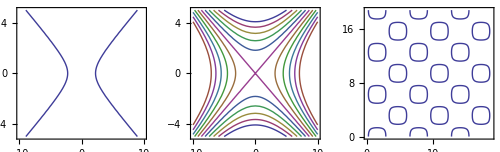

```mathematica
GraphicsRow[{
ContourPlot[x^2-3 y^2==5,{x,-10,10},{y,-5,5}],
ContourPlot[Evaluate[Table[x^2-3 y^2==k,{k,-50,50,10}]],{x,-10,10},{y,-5,5}],(* contour map *)
ContourPlot[Sin[x]Cos[y]==1/4,{x,0,6Pi},{y,0,6Pi}]},
Spacings->50,ImageSize->500]
```

Move the cursor around over the central contour map. At any point (x,y) in the region covered by level curves, you can estimate what is the value of z=f(x,y)=x^2-3 y^2 at the point, the third dimension, z, on such a 2-D graph, which is what a contour map is for.

Note: Evaluate[expr] causes expr to be evaluated. You can do experiment with this example by removing it and see what will happen.

Animation can be made with ContourPlot, too. Run the following code and play with the sliders so as to find some specific equations which define curves of cool shapes. For example, the curve of (0.15 x^2+1.35 y^2)^2.2=-2.5x+3.2x y+1.2 is pretty nice.

```mathematica
Manipulate[
Show[{
ContourPlot[(a x^2+b y^2)^n==c x+d x y+e y+f,{x,-10,10},{y,-10,10},ImageSize->300],
Graphics[Text[StringJoin["n = ",ToString[n]],{-8,9.5}]],
Graphics[Text[StringJoin["a = ",ToString[a]],{-8,8.5}]],
Graphics[Text[StringJoin["b = ",ToString[b]],{-5,8.5}]],
Graphics[Text[StringJoin["c = ",ToString[c]],{-2,8.5}]],
Graphics[Text[StringJoin["d = ",ToString[d]],{-8,7.5}]],
Graphics[Text[StringJoin["e = ",ToString[e]],{-5,7.5}]],
Graphics[Text[StringJoin["f = ",ToString[f]],{-2,7.5}]]
}],{{n,2.71},1,10},{a,0.1,3,0.1},{b,0.1,3,0.1},{c,-3,3,0.1},{d,-3,3,0.1},{e,-3,3,0.1},{f,-3,3,0.1}]
```

Example 4
Given that x^2+y^2=1, plot the equation together with the tangent line(s) at x=0.5.

To plot the tangent lines, we need to find first their slopes, y'(3) for setting up their equations.

```mathematica
Clear[x,y,eqn]
eqn[x_,y_]:=x^2+y^2==1
x0=0.5;
yPrime=(y'[x]/.Solve[D[eqn[x,y[x]],x],y'[x]])[[1]]/.y[x]->y
```

-x/y

```mathematica
ys=NSolve[eqn[x,y]/.x->x0,y]
```

{{y→-0.866025},{y→0.866025}}

Corresponding to x=0.5, there are two points, i.e., (0.5,±0.866025). The slopes at the points are

```mathematica
ms=yPrime/.ys/.x->x0
```

{0.57735,-0.57735}

Therefore, the two tangent lines are y=-0.866025+0.57735(x-0.5) and y=0.866025-0.57735(x-0.5). Finally,

```mathematica
y0s=y/.ys
```

{-0.866025,0.866025}

2

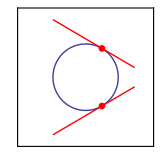

```mathematica
numOfY0s=Length[y0s]
Show[{
ContourPlot[Evaluate[eqn[x,y]],{x,-2,2},{y,-2,2},FrameTicks->None,ImageSize->160],
Graphics[Table[{PointSize[0.03],Red,Point[{x0,y0s[[i]]}]},{i,1,numOfY0s}]],
Plot[Table[y0s[[i]]+ms[[i]](x-x0),{i,1,numOfY0s}],{x,-1,1.5},PlotStyle->{{Red}}]}]
```

Example 5
One more example. It shows how to combine all steps scattered in cells in Example 4 into a single Mathematica function that reduces the need of user’s intervention in a computing process. It is always a good practice to use variables to replace numbers as much as possible since it improves the generality and, thus, the reusability of the code.

```mathematica
Plot2DEqnAndTangentLines[equation_,x0_,{x_,xmin_,xmax_},{y_,ymin_,ymax_}]:=Module[
{eqn,yPrime,ys,ms,y0s,numOfY0s},(* local variables *)

eqn[X_,Y_]:=equation/.{x->X,y->Y};(* a necessary step *)
yPrime=(y'[x]/.Solve[D[eqn[x,y[x]],x],y'[x]])[[1]]/.y[x]->y;
ys=NSolve[(eqn[x,y]/.x->x0)&&ymin≤y≤ymax,y]//Quiet;
ms=yPrime/.ys/.x->x0;
y0s=y/.ys;
numOfY0s=Length[y0s];
Show[{
ContourPlot[Evaluate[eqn[x,y]],{x,xmin,xmax},{y,ymin,ymax},Frame->False],
Graphics[Table[{PointSize[0.03],Red,Point[{x0,y0s[[i]]}]},{i,1,numOfY0s}]],
Plot[Table[y0s[[i]]+ms[[i]](x-x0),{i,1,numOfY0s}],{x,xmin,xmax},PlotStyle->{{Red}}]
}]
]
```

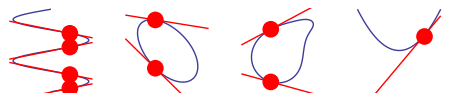

```mathematica
GraphicsRow[{
Plot2DEqnAndTangentLines[s==Sin[t],0.5,{s,-1.1,1.1},{t,-2π,2π}],
Plot2DEqnAndTangentLines[(2 x^2+0.5 y^2)^1.14==2.7x-2.4x y-3y-2.3,1,{x,-1,4.55},{y,-9.4,1}],
Plot2DEqnAndTangentLines[(0.15 x^2+1.35 y^2)^2.2==-2.5x+3.2x y+1.2,-3,{x,-6,2.5},{y,-1.8,1.3}],
Plot2DEqnAndTangentLines[y==x^2,1.2,{x,-2,2},{y,-4,4}]
},Spacings->50,ImageSize->450]
```

## Related rates

Assume that two variables x and y satisfy an equation in some way, for example, x^2+y^2=1, y=π x^2, and y=x ⅇ^x, and they are each a function of a third variable t, i.e., x=x(t) and y=y(t). The problem is, given x'(t) (or y'(t)) at x=x_0, how to find y'(t) (or x'(t)) at the point. Here, x'(t) and y'(t) are called the related rates of change with respect to t.

Applying implicit differentiation technique, we can solve the problem in just a few steps.

Example 6
A circle is expanding. If the radius is increasing at the rate of 2 cm/s, at what rate is the area increasing when the radius is 10 cm?

Let r and A denote the radius and the area of the circle, respectively. The relation between the two variables is A=π r^2.

Now, at the point r=10, given that (d r)/(d t)=2, what is (d A)/(d t)?

```mathematica
eqn=A==π r^2;
D[eqn/.{r->r[t],A->A[t]},t]
```

A'[t]==2 π r[t] r'[t]

```mathematica
dAdt=(A'[t]/.Solve[%,A'[t]] /.{A[t]->A,r[t]->r,r'[t]->r'}//Simplify)[[1]]
```

2 π r r'

```mathematica
dAdt/.{r->10,r'->2}
```

40 π

Thus, the area is increasing at rate of 40π cm^2/s.

Example 7
Refer to example 6. Given that the area is increasing at the rate of 30 cm^2/s when the area is 50π cm^2, at what rate is the radius increasing corresponding?

```mathematica
eqn=A==π r^2;
D[eqn/.{r->r[t],A->A[t]},t];
drdt=(r'[t]/.Solve[%,r'[t]]/.{A[t]->A,A'[t]->A',r[t]->r}//Simplify)[[1]]
```

A'/(2 π r)

To evaluate r'(t)=A'/(2π r), we still need to know r when the area is 40π cm^2. It can be found by

```mathematica
rs=r/.Solve[eqn,r]/.{A->40π}//N
```

{-6.32456,6.32456}

Since a radius can never be negative, r≈6.32456. Therefore,

```mathematica
drdt/.{r->rs[[2]],A'->30}
```

0.754938

Therefore, the radius is increasing at the rate of about 0.7549 cm/s.

## Taylor polynomials and approximation

According to Taylor’s Theorem, if f(x) has all continuous derivatives on an open interval I that contains the point x=a, then for every x∈I

f(x)=f(a)+f'(a)(x-a)+(f''(a))/(2!)(x-a)^2+(f'''(a))/(3!)(x-a)^3+⋯ or f(x)=∑_(n=0)^∞ (f^(n)(a))/(n!)(x-a)^n.

P_n(x)=f(a)+f'(a)(x-a)+(f''(a))/(2!)(x-a)^2+(f'''(a))/(3!)(x-a)^3+⋯+(f^(n)(a))/(n!)(x-a)^n is the n-th degree Taylor polynomial of f(x) at x=a. We can use P_n(x) to approximate f(x) near x=a, and a larger n gives a better approximation. Especially,

P_1(x)=f(a)+f'(a)(x-a)

P_2(x)=f(a)+f'(a)(x-a)+(f''(a))/(2!)(x-a)^2

P_3(x)=f(a)+f'(a)(x-a)+(f''(a))/(2!)(x-a)^2+(f'''(a))/(3!)(x-a)^3

are called the linear, quadratic, and cubic approximations to f(x) at x=a, respectively.

Note: Using differentials to estimate f(x) is actually use P_1(x) to approximate f(x). Provided f(x) is differentiable at x and d x=△ x=h is sufficiently small, △ y≈d y=f'(x)d x=f'(x)△ x, or f(x+h)-f(x)≈f'(x)h. Thus, f(x+h)≈f(x)+f'(x)h. At x=a, this is f(a+h)≈f(a)+f'(a)h. Now, letting x=a+h, we have f(x)≈f(a)+f'(a)(x-a)=P_1(x).

Example 8
This example plots ⅇ^x and its first twenty Taylor polynomials in powers of x. We can see that the higher the degree of the Taylor polynomial is, the better approximation the polynomial produces.

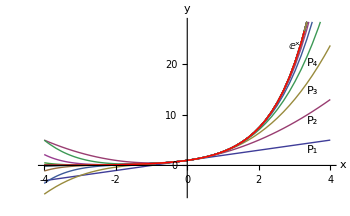

```mathematica
Block[{f,a,fs,P},
f[x_]:=Exp[x];
a=0;
P[x_,n_]:=f[a]+Total[Table[(D[f[x],{x,i}]/.x->a)/(i!)(x-a)^i,{i,1,n}]]//Simplify;
fs=Table[P[x,n],{n,1,20}];
Show[{
Plot[fs,{x,-4,4},Ticks->{{-4,-2,0,2,4},{0,10,20}},AxesLabel->{x,y},ImageSize->350],
Plot[f[x],{x,-4,4},PlotStyle->{{Red,Thick}}],
Graphics[Text[Subscript[P, 1],{3.5,3.1}]],
Graphics[Text[Subscript[P, 2],{3.5,8.7}]],
Graphics[Text[Subscript[P, 3],{3.5,14.7}]],
Graphics[Text[Subscript[P, 4],{3.5,20.2}]],
Graphics[Text[f[x],{3,23.5}]]
}]]
```

Which one, Block or Module, should we use? In most cases, either one works well in using and hiding symbols (see Unit 4). But in this very example, if Module is used, P can not be put into the list of “local” symbols. If P is a global variable, Clear[P] or similar command must be executed before Block and Module.

The difference between Module and Block is not very obvious. One thing is clear, Block can do more in the sense that it can be used to provide an environment in which the values of symbols, including global ones, can temporarily be changed, and at the end, their original values are restored automatically. While Module internally changes the name of a symbol, e.g., from x to x$6355, Block does not. For example,

```mathematica
x=100;Module[{Sin,x,y},{Sin[π/2],x,y}]
```

{Sin$13560[π/2],x$13560,y$13560}

Module has a local version of a symbol if the symbol is in the list of local symbols, such as Sin$7010 and x$7010. In Module, if a local symbol is assigned a value, the assigned value is used; otherwise, the symbol has no associated value.

```mathematica
x=100;Module[{Sin=Cos,x=1,y},{Sin[π/2],x,y}](* Sin[x] is temporarily changed to be Cos[x] *)
```

{0,1,y$13561}

```mathematica
x=100;Block[{Sin,x,y},{Sin[π/2],x,y}]
```

{1,100,y}

Block does not have a local version of any symbol. In Block, if a local symbol is assigned a new value, the new value is used; otherwise, the original global value is still valid and, thus, used.

```mathematica
x=100;Block[{Sin=Cos,x=1,y},{Sin[π/2],x,y}] (* Sin[x] is temporarily changed to be Cos[x] *)
```

{0,1,y}

The next example defines a recursive function for computing 1+2+3+⋯+n.

```mathematica
sum[n_]:=If[n==1,1,n+sum[n-1]]
{sum[1],sum[10],sum[100]}
```

{1,55,5050}

The evaluation of sum[10] is expanded recursively as 10+(9+(8+(7+(6+(5+(4+(3+(2+1))))))))=10+(9+(8+(7+(6+(5+(4+(3+3)))))))= ⋯=10+45=55.

To prevent a recursive function from using up computer resource, both processor time and memory, Mathematica uses a built-in global variable, $RecursionLimit, to monitor the recursion depth. Its value is 256 by default, which does not allow the evaluation of, say, sum[1000]. But we can change its value to meet our needs. However, it is not a good practice to randomly change the value of this global variable. Instead, we should think of designing a non-recursive algorithm.

 For example,

```mathematica
Block[{$RecursionLimit=10003},{sum[10],sum[100],sum[1000],sum[10000]}]
```

{55,5050,500500,50005000}

Block is automatically used to localize values of iterators in iteration constructs such as Table, Plot, Manipulate, Animate, Do, Sum, and so on. For example,

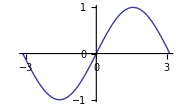

```mathematica
aGlobalVariable$06$25$2015="Old value";
Plot[Sin[aGlobalVariable$06$25$2015],{aGlobalVariable$06$25$2015,-Pi,Pi},ImageSize->180]
```

```mathematica
Manipulate[Sin[aGlobalVariable$06$25$2015*x],{{aGlobalVariable$06$25$2015,1,"n"},1,10,1},Alignment->Center]
```

```mathematica
Table[Prime[aGlobalVariable$06$25$2015],{aGlobalVariable$06$25$2015,1,10}]
```

{2,3,5,7,11,13,17,19,23,29}

```mathematica
aGlobalVariable$06$25$2015 (* This global variable has been used several times, and its value seems to have be changed. But it still holds the same value. *)
```

Old value

Example 9
Use a differential to estimate √99.

Choose f(x)=√x at x=100, and estimate f(99). Differential d x=△ x=99-100=-1, and differential d f=f'(x)d x is used to approximate △ y, the increment in y as x changes from 100 to 99.

```mathematica
f[x_]:=√x
dx=99-100;
df=f'[x]dx/.x->100
```

-1/20

Now, △ y=f(99)-f(100)≈d f, or f(99)≈f(100)+d f.

```mathematica
f[100]+df//N
```

9.95

Example 10
Find the linear approximation of f(x)=ⅇ^x at x=2. Then, use it to approximate f(2.05).

```mathematica
f[x_]:=E^x
a=2;
P1[x_]:=f[a]+f'[a](x-a)//Simplify
```

```mathematica
P1[2.05]
```

7.75851

The absolute error of the approximation is

```mathematica
Abs[f[2.05]-%]
```

0.0093922

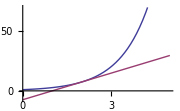

```mathematica
Plot[{f[x],P1[x]},{x,0,5},ImageSize->180]
```

Example 11
Find the quadratic approximation of f(x)=ⅇ^x at x=2. Then, use it to approximate f(2.05).

```mathematica
f[x_]:=E^x
a=2;
P2[x_]:=f[a]+f'[a](x-a)+f''[a]/2(x-a)^2//Simplify
```

```mathematica
P2[2.05]
```

7.76775

```mathematica
Abs[f[2.05]-%] (* absolute error *)
```

0.000155882

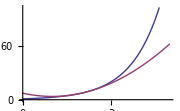

```mathematica
Plot[{f[x],P2[x]},{x,0,5},ImageSize->180]
```

Example 12
Find the cubic approximation of f(x)=ⅇ^x at x=2. Then, use it to approximate f(2.05).

```mathematica
f[x_]:=E^x
a=2;
P3[x_]:=f[a]+f'[a](x-a)+f''[a]/2(x-a)^2+f'''[a]/6(x-a)^3//Simplify
```

```mathematica
P3[2.05]
```

7.7679

```mathematica
Abs[f[2.05]-%] (* absolute error *)
```

1.94364×10^-6

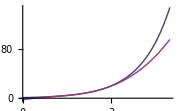

```mathematica
Plot[{f[x],P3[x]},{x,0,5},ImageSize->180]
```

## Newton’s method

It’s also called Newton-Raphson method. It is used to find a root of a function.

The idea is as follows.
(1) Begin with an initial guess, x_1, of the root. (Rename it as x_i, where i=1.)
(2) Draw the tangent line to f(x) at (x_i,f(x_i)). Its equation is given by y=f(x_i)+f'(x_i)(x-x_i).
(3) The foregoing tangent line intersects the x-axis at x_(i+1): 0=f(x_i)+f'(x_i)(x_(i+1)-x_i), or

x_(i+1)=x_i-(f(x_i))/(f'(x_i))⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯(1)

(4) If f(x_(i+1)) is sufficiently close to zero, x_(i+1) is a root. Otherwise, let i be i+1, and go to step (2).

Under certain conditions like f(x),f'(x) and f''(x) are continuous near a root, the sequence {x_1,x_2,x_3,⋯} converges to the root very fast. However, as we can see from (1), if f'(x) is close to zero near the root, the sequence may converge very slowly or even diverge.

The following code and the graph exhibit the idea of the method.

Usage:

func, function to be explored.

x1: initial guest of the root of func.

count: number of iterations for generating the sequence of approximations, x_1,x_2,x_3,⋯, used by NestList.

fLabelPos: coordinates of position where func is printed on the graph, e.g., {10,8.5}.

labelY: y-coordinate of x_1,x_2,x_3,⋯ plotted on the graph.

labelCount: meaningful number of x_1,x_2,x_3,⋯ plotted on the graph. It is usually a small number. If it is large, symbols may be covered by other symbols.

ticks: E.g., ticks→{{-2,0,2},{-1,0,10}}.

```mathematica
ExploreNewtonMethod[func_,x1_,count_,fLabelPos_, labelY_,labelCount_,{x_,xmin_,xmax_},{y_,ymin_,ymax_},ticks_]:=Module[
{f,nestF,xs,tangentLines,vertLines,labels},

f[X_]:=func/.x->X;
nestF[xi_]:=xi-f[xi]/f'[xi]//N;
xs=NestList[nestF,x1,count];
tangentLines=Table[f[xs[[i]]]+f'[xs[[i]]](x-xs[[i]]),{i,1,Length[xs]}]//Simplify;
vertLines = Table[Line[{{xs[[i]],0},{xs[[i]],f[xs[[i]]]}}],{i,1,Length[xs]}];
labels = {Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6],Subscript[x, 7] Subscript[x, 8],Subscript[x, 9],Subscript[x, 10],Subscript[x, 11],Subscript[x, 12]}; (* we don't need that many. but in case ... *)

Show[{
Plot[tangentLines,{x,xmin,xmax},PlotRange->{ymin,ymax},
PlotStyle->{Black},ticks,AxesLabel->{x,y},ImageSize->350],
Plot[f[x],{x,xmin,xmax},PlotStyle->{Red,Thickness[0.01]}],
Graphics[Text[f[x],fLabelPos]],
Table[Graphics[Text[labels[[i]],{xs[[i]],labelY}]],{i,1,labelCount}],(* Length[xs]? jammed! *)
Graphics[{Dashed, vertLines}],
Graphics[Table[{PointSize[0.02],Blue,Point[{xs[[i]],0}]},{i,1,Length[xs]}]]
}]]
```

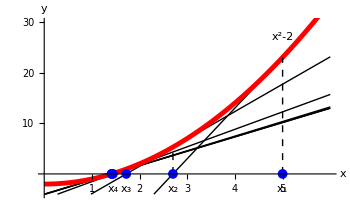

```mathematica
Clear[x]
ExploreNewtonMethod[x^2-2,5,5,{5,27},-3,4,{x,0,6},{y,-4,30},Ticks->{{1,2,3,4,5},{10,20,30}}]
```

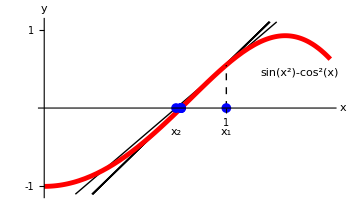

```mathematica
ExploreNewtonMethod[Sin[x^2]-Cos[x]^2,1,5,{1.4,0.45},-0.3,2,{x,0,Pi/2},{y,-1.1,1.1},Ticks->{{1,2},{-1,1}}]
```

Example 13
Use Newton’s method to find the root of f(x)=x^7+4 x^6+3 x^5-2 x^4-2 x^3-12 x^2-8 x+16.

First, we plot the graph of the function so as to form an initial guess to each root.

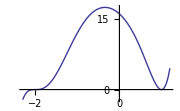

```mathematica
f[x_]:=x^7+4 x^6+3 x^5-2 x^4-2 x^3-12 x^2-8 x+16
Plot[f[x],{x,-2.3,1.2},ImageSize->180] (* we started from {x, -100, 100}, and gradually narrowed down to this interval which makes the graph clear and cool -:) *)
```

```mathematica
newton[x_]:=x-f[x]/f'[x]
```

```mathematica
NestList[newton,-1.9,10] (* find the root close to -1.9 *)
```

{-1.9,-1.93492,-1.95727,-1.97179,-1.98132,-1.9876,-1.99175,-1.99451,-1.99635,-1.99757,-1.99838}

It seems that -2 is one root, and it is.

```mathematica
f[-2]==0
```

True

```mathematica
NestList[newton,0.9,6] (* find the root close to 0.9 *)
```

{0.9,0.95457,0.978181,0.989293,0.994695,0.997359,0.998682}

x=1 looks like a root. We can verify that it is.

```mathematica
f[1]
```

0

Usually, a fast convergent algorithm needs only a few iterations to find a root. The root x=-2 in this example needs more steps because f'(x) is close to zero near the root. Zooming in at the two roots below confirms the explanation.

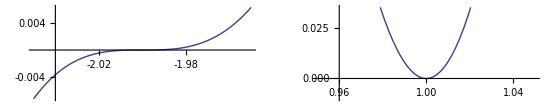

```mathematica
GraphicsRow[{
Plot[f[x],{x,-2.05,-1.95},Ticks->{{-2.02,-2,-1.98,-1.96},{-0.004,0.004}},AspectRatio->Automatic],
Plot[f[x],{x,0.95,1.05},AspectRatio->Automatic,PlotRange->{-0.01,0.035}]
},ImageSize->550]
```

© 2015-2024 by David Wang, dwang@liberty.edu